# FAQ : Causal Networks

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

Causal Networks:

Currently the best description of how a causal is constructed from a sessie is in the Caviness, Beard, ________ & Deschamps paper.

Anyone want to help mine pieces of that explanation to create this FAQ?
Or to start building a nice animated explanation, similar to Jade Deschamps’ PPT in the Repo “Intro-Documents”

Thoughts on how to build an animated explanation (Colton Edelbach)
In order to build an animated  explanation similar to Jade Deschamps PPT, we need the “Sessie”, the gray and red boxes, to grow in length and not in width. We also need the network to grow without changing (The whole network needs to be present, just the parts that we don’t want to see should be invisible). This means we need to animate the network so that at every integer, n, any numbers less than or equal to n are shown and any integers greater than n are invisible. We also need to make sure that the connections between the numbers greater than n are not shown. This could be done by making all the numbers greater than “n” white, or if there is a command to make them not appear that would work too. 

From <https://github.com/orgs/sessieresearchatsau/repositories>

Probably this would be based on adapting SSSAnimate, which needs to be fixed anyway, to allow more options. A new option might either replace vertices & edges after a specified number by white (invisible) versions (similar to the current behavior in changing all but one vertex to an unlabeled Point), or generated the Net, make note of all VertexCoordinates, and redisplay a subset of the Net with the same coordinates.

In either case, we also want the colored box picture to grow one line at a time, with lines 0-n showing in the SSS when vertices 1-n are shown in the Net, and we don’t want things to move around or greatly resize. It might be nice to have the latest vertex still in green, and the last one or two lines of the SSS boxed in green, since the event (vertex) was the application of a rule to make that last change in the SSS state string.

#### Causal Networks

A causal network, also known as a Bayesian network, is a graphical model that is used to represent the relationship between two or more variables. This network typically consists of nodes, which represent variables, and edges connecting these nodes,  which represent causal influences between them. This means that any two nodes connected together will have some dependency on each other (or one node is dependant on the parent node) while two nodes not connected are independent of each other. Causal networks are different from other networks due to these lines as they indicate causality between the nodes rather than just indicating that they are associated.

```mathematica
(-Graphics-)^□
```

Figure 1: An example of a simple Bayesian network

Figure 1 is a basic example of a causal network, as indicated by the nodes (rain, sprinkler, wet grass) and the lines indicating the relationship between them. Rain has an effect on both the sprinkler (turning it off) and the wet grass (making it wet), as indicated by the arrows, while sprinklers only have an effect on wet grass. Because wet grass is only affected by the other nodes, it is strictly dependent and causes no change in the others.

#### Causality vs Correlation

When building a causal network, it is important to be able to differentiate between causation and correlation as correlation does not imply causation. In the absence of enough scientific research, it can be necessary to draw causal inferences from observational data, but doing this accurately can be challenging. While comparing variables it is necessary to differentiate between weather an event/variable actually causes a specific outcome or weather it is merely correlated. Looking back at Figure 1, we know that rain falling directly causes the grass to get wet, allowing us to conclude that there is a causal relationship between them. However, if we tried to draw a causal network between the presence of wet grass and the use of umbrellas, this would be an example of correlation and not causation. Wet grass and people using umbrellas are both effects of rain falling and are not directly affected by each other. When constructing causal networks it is important to verify that your two variables are truly affected by each other and that a confounding variable is not affecting your judgment.

#### Applications of Causal Networks

Causal networks can be useful in a variety of fields including determining the causal factors for disease in medicine, the effects of environment changes on ecosystems, developing artificial neural networks, and many other examples.

#### Causal Networks of Sequential Substitution Systems

The causal network shown for a Sessie (SSS) is built from a study of which cells in the colored picture are created and destroyed by which events. The creation of a cell must precede its destruction. This is taken as a model for a causal connection of any type.  In this example, 25 steps in the “toy universe” are shown: 25 lines of colored boxes — giving a quick view of the changing state string, and 25 vertices (or events) in the causal network.



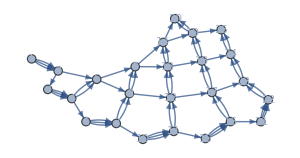
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss1 = SSS[{"ABA"->"AAB","A"->"ABA"},"AB",25, RulePlacement->Left, SSSSize -> 100, NetSize -> 300];
```

In this example event 1 created three cells which event 2 destroyed. This lead to the three connections between events 1 and 2. Event 2 created a cell which was destroyed by event 3 and another which was destroyed by event 5, etc. The creation and destruction of cells may be determined from the colored Sessie picture but the same color does not necessarily mean the same cell. All grey boxes mean there was an “A” in the state string. To differentiate one “A” from another, our code assigns a unique tag to each cell. Use TEvolution to see the tags.

```mathematica
sss1[["Evolution"]][[{1,2,3,4,5}]]//Column
```

"AB"
"A"
"AABB"
"ABAABB"
"AABABB"

```mathematica
sss1[["TEvolution"]][[{1,2,3,4,5}]]//Column
```

s[{0,1},{1,2}]
s[{0,3},{1,4},{0,5},{1,2}]
s[{0,6},{0,7},{1,8},{1,2}]
s[{0,9},{1,10},{0,11},{0,7},{1,8},{1,2}]
s[{0,12},{0,13},{1,14},{0,7},{1,8},{1,2}]

```mathematica
Grid[
Prepend[
Transpose@{sss1[["Evolution"]][[{1,2,3,4,5}]],
sss1[["TEvolution"]][[{1,2,3,4,5}]]},
Style[#,{"Subsubsection",Underlined}]&/@{"Evolution","Tagged Evolution"}],
Alignment->Left,Spacings->{5,0.5}
]
```

Evolution | Tagged Evolution
AB | s[{0,1},{1,2}]
ABAB | s[{0,3},{1,4},{0,5},{1,2}]
AABB | s[{0,6},{0,7},{1,8},{1,2}]
ABAABB | s[{0,9},{1,10},{0,11},{0,7},{1,8},{1,2}]
AABABB | s[{0,12},{0,13},{1,14},{0,7},{1,8},{1,2}]

Both the list of state strings in the “Evolution” and the sequence of S-objects in “TEvolution” represent the development of the toy universe, but the “tagged” evolution gives more detail:  The first number in each S-object identifies which character of the alphabet is referred to: “A”, “B”, etc.  In our example, {0, _} identifies the letter “A”, {1, _} means “B”, etc. The second number in the S-object pair is a unique tag that is specific to each unique “A” or “B”, a personal identifier that allows us to differentiate between cases with the same letter.  So the first “A” is {0,1}; no other distinct “A” has the same tag (1). In line two, there are two “B” characters ({1,4} and {1,2}). In our example, we can see that the only letter that does not get destroyed is the last “B” in the evolution. We can trace it in the tagged evolution by following its identifier, {1, 2}, as it progresses through multiple events. Using the information from the TEvolution, we can see that a “B” only becomes permanent in this universe once it arrives at the end of the string. Only the cells that were created and destroyed appear as arrows on the causal network graph, connecting the creation event and the destruction event. This means that the “B”s at the end of the state string will not appear in our causal network: it was primordial -- never created, and it is never destroyed. The causal connections that we display in the graph are limited to creation and destruction of cells. Clearly a cell cannot be destroyed before it is created. This gives a natural ordering of the events in the network.

#### Timely Musings

In the colored picture of our example, time flows downwards. Since each row corresponds to an application of a rule, and nothing happened in between these applications, this can be considered the smallest unit of time (Planck time!) in our universe. The causal network; however, gives a different view of time. Events 4, 5, 9, and 13 occurred sequentially because the network shows arrows from 4 to 5, 5 to 9 and from 9 to 13. This could be called macro-time in contrast to micro-time which included all events in numerical order. An alternative path to get from 4 to 13 is to go from 4 to 6, 6 to 7, 7 to 10, 10 to 11, 11 to 12, and 12 to 13, which represents six units of macro-time, rather than 3. There are also three other paths to get from 4 to 13 as it could progress from.

1. 4 to 5, 5 to 8, 8 to 12, and 12 to 13 (4 units of macro-time)
2. 4 to 6, 6 to 7, 7 to 8, 8 to 9, and 9 to 13 (5 units of macro-time)
3. 4 to 6, 6 to 7, 7 to 8, 8 to 12, and 12 to 13 (5 units of macro-time)

This toy universe has the relativity of time like our universe. Different observers can experience different time intervals, macro-time,  between the same pair of events. For instance, an observer going from 4 to 13 in this network has five ways of getting there, each with their own different amounts of (macro-) time.  Depending on the path taken it can either take as little as 3 units to as many as 6 macro-time units. This can be thought of stretching the causal network in various ways, without detaching any of the connections.

The connections between the nodes can be thought of as worldlines for some observer. Any events that occur on one observer’s worldline cannot be temporally reversed, as their order is fixed. Macro-time is based on the causal connections between nodes. Nodes that are not connected cannot be differentiated in time, meaning we have no way of defining one of these events as earlier or later than the other. For example, the events 9 and 12 occur on the two different mentioned paths, but are not connected. Except in relation to particular observer, it is meaningless to claim either one as “earlier” in macro-time.

#### FAQ Sessie Intro, 2025.03.05, Kenneth Caviness and Colton Edelbach